```mathematica
rawdata=Table[Import["/Users/WillC/Documents/Rutgers/Research/RADICAL/Minions/data/output/test"<>ToString[x]<>"/data"<>ToString[x]<>".csv"][[All,All]],{x,7,13}]
```

{{{8,8,300.329}},{{8,16,600.552}},{{8,32,1201.18}},{{8,64,2402.28}},{{8,128,4804.29}},{{8,256,9608.49}},{{8,512,19216.7}}}

#### ILAB 8-Core Test Plot

```mathematica
sleepseconds=300;
ilabtime=Table[{sleeptime*rawdata[[x]][[1]][[2]]/rawdata[[x]][[1]][[1]],rawdata[[x]][[1]][[3]]},{x,1,Length[rawdata]}];
ilabjob=Table[rawdata[[x]][[1]][[2]],{x,1,Length[rawdata]}];
ilabjobString=Table[ToString[rawdata[[x]][[1]][[2]]],{x,1,Length[rawdata]}];
ilaboverhead=Table[Abs[sleeptime*rawdata[[x]][[1]][[2]]/rawdata[[x]][[1]][[1]]-rawdata[[x]][[1]][[3]]],{x,1,Length[rawdata]}];
```

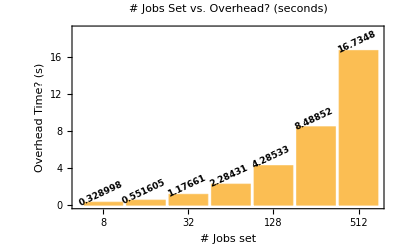

```mathematica
overhead = BarChart[ilaboverhead,ChartLabels->ilabjobString,LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),Frame->True,FrameLabel->{"# Jobs set","Overhead Time? (s)"},PlotLabel->"# Jobs Set vs. Overhead? (seconds)",PlotRange->{All,{0,19}}]
```

```mathematica
sidebyside=BarChart[ilabtime,ChartLabels->{ilabjobString,{"expected","meas."}},LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),Frame->True,FrameLabel->{"# Jobs set","Time (s)"},PlotLabel->"# Jobs Set vs. Time (seconds)",PlotRange->{All,{0,20500}}]
```

```mathematica
Roverhead=Rasterize[overhead,ImageResolution->200]
Rsidebyside=Rasterize[sidebyside,ImageResolution->500]
```

#### Linear Fit

```mathematica
lm = LinearModelFit[avgPoints,x,x];
Normal[lm]
```

```mathematica
Normal[lm]
```

86.0805-10.4321 x

```mathematica
standardError[ts_]:=StandardDeviation[ts]/Abs[ts]
```

```mathematica
stderr=standardError[avgPoints[[All,2]]]
stderr=Table[{avgPoints[[i,1]],avgPoints[[i,2]],stderr[[i]]},{i,1,3}]
```

{0.211747,0.242451,0.360908}

{{1,75.2895,0.211747},{2,65.7549,0.242451},{4,44.1728,0.360908}}

```mathematica
points=ListPlot[avgPoints,PlotRange->{{0,5},All},PlotMarkers->{Automatic,Small},PlotStyle->{Black,Opacity[0.5]}];

fit=Plot[lm[x],{x,0,5},PlotStyle->{Gray,Dashed},PlotLegends->{"Linear Fit\n"<>ToString[Normal[lm]], FontSize->12}];

Needs["ErrorBarPlots`"]
errplot=ErrorListPlot[stderr,PlotMarkers->{".",Tiny},PlotStyle->{Blue}];

final=Show[{fit,errplot(*,points*)},Frame->True,FrameLabel->{"# cores set","Time (s)"},LabelStyle->Bold,PlotLabel->"# Cores vs. Average MonteCarlo Runtimes",PlotRange->{All,{40,80}}]
```